Read me

This notebook can be used to reproduce the results shown in panel a of Fig. 5 of “Online quantum time series processing with random oscillator networks” (https://arxiv.org/abs/2108.00698) in the manner described in the preprint. It requires a working installation of a recent version of Wolfram Mathematica. It has been tested in Wolfram Mathematica 11.2 for Microsoft Windows (64-bit). 

To use it, evaluate Sections 1 and  2.1 first. The parameter “realizations” controls how many samples are used to generate the ensemble averages and is by default set to 10. In “Online quantum time series processing with random oscillator networks” a value of 100 has been used.

Then you can proceed either with 2.2. Inside this subsection cells should in general be evaluated in order, i.e. plots can be made only after data has been generated and so on. Subsection 2.3 only contains results computed previously, to reproduce these computations use the notebook Figure 5b partial generalizations.

Both 2.2 and 2.3 need to be evaluated before 2.4 which simply combines the results into a single figure. 

The author of this notebook is Johannes Nokkala. Any inquiries about its contents can be sent to jsinok@utu.fi

Summary of the license
This work is licensed under CC BY 4.0. You are free to share and adapt the material as long as it remains under the same license  and you give appropriate credit. For the full legal text see LICENSE in the main repository: https://github.com/jsinok/onlinequantumtimeseries

1 Preliminaries

We will clear all values, definitions, attributes, messages, and defaults associated with symbols in the global context. This is to prevent problems with pre-existing symbol definitions.

```mathematica
ClearAll["Global`*"];
```

We will set the history length to 0 to keep memory consumption in check. That is to say none of the previous input and output lines are saved by default for later use, only the ones we explicitly keep.

```mathematica
$HistoryLength=0;
```

Parallelization is used to speed up certain parts of the computations. We launch the maximum number of them now.

```mathematica
If[$ProcessorCount-$KernelCount>0,LaunchKernels[$ProcessorCount-$KernelCount]]
```

## User-defined functions

### Auxiliary

#### Permutations

```mathematica
(*permutes qqq..ppp.. to qpqpqp..*)
getmatP=Function[m,IdentityMatrix[2m,WorkingPrecision->MachinePrecision][[Riffle[Range[m],Range[m]+m]]]];
```

#### Visualization

These ones are for array and matrix plots you know.

```mathematica
getcoords=Function[{dim,index},Scaled[{(Last[index]-0.5)/Last[dim],1-(First[index]-0.5)/First[dim]}]];
```

```mathematica
getarraylabels=Function[{ar,sty},MapIndexed[Text[Style[#1,sty],getcoords[Dimensions[ar],#2]]&,ar,{2}]];
```

```mathematica
makearraylabels=Function[{ar,round,sty},Epilog->getarraylabels[Round[ar,round],sty]];
```

#### Graphs

```mathematica
Clear[completegraphrandomweights];
completegraphrandomweights[n_]:=SetProperty[CompleteGraph[n],EdgeWeight->{_:>RandomReal[{0.,2.}]}];
```

```mathematica
Clear[weightedKirchhoffMatrix];
weightedKirchhoffMatrix[g_]:=DiagonalMatrix[Tr/@Transpose@#]-#&@WeightedAdjacencyMatrix[g]
```

### State related

#### Random single mode state generator

```mathematica
Clear[getσthsqz];
getσthsqz[nthermal_,r_,φ_,ωbare_]:=ConstantArray[nthermal+0.5,{2,2}]×{{ωbare^-1 (Cosh[2 r]+Cos[φ] Sinh[2 r]), Sin[φ] Sinh[2 r]},{ Sin[φ] Sinh[2 r], ωbare (Cosh[2 r]-Cos[φ] Sinh[2 r])}};
```

#### Initial reservoir state generator

```mathematica
(*init covariances in the qqq..ppp.. basis*)
getinitσ=Function[{temperature,matrixK,listΩ},With[{matrixKbig=KroneckerProduct[N@IdentityMatrix[2],matrixK],listnplushalf=If[temperature>0,(Exp[listΩ/temperature]-1)^-1+0.5,ConstantArray[0.5,Length[listΩ]]]},matrixKbig.DiagonalMatrix[Join[listnplushalf/listΩ,listΩ listnplushalf]].matrixKbigᵀ]];
```

### Hamiltonian related

#### Reservoir generator

```mathematica
(*input: graph, uniform coupling strength, bare frequency*)
(*output: matrix defining the Hamiltonian of a network of identical oscillators with the bare frequency, interacting with uniform coupling strengths; orthogonal matrix diagonalizing the previous matrix; frequencies in the diagonal basis*)
Clear[getmatrixA];
getmatrixA=Block[{matrixA=DiagonalMatrix[ConstantArray[#3^2 /2,VertexCount[#1]]]+#2 weightedKirchhoffMatrix[#1]/2,listK,listD},
{listD,listK}=Eigensystem[matrixA];
{matrixA,Transpose[Normalize/@listK],√(2listD)}]&;
```

Returns the initial covariance matrix in the qpqpqp ordering!

```mathematica
Clear[getrandomreservoir];
getrandomreservoir[n_,ωbare_,g_]:=With[{matrixHmatrixKlistΩ=getmatrixA[completegraphrandomweights[n],g,ωbare]},
{First[matrixHmatrixKlistΩ],
With[{matrixPermute=getmatP[n]},matrixPermute.getinitσ[0.,matrixHmatrixKlistΩ[[2]],Last[matrixHmatrixKlistΩ]].matrixPermuteᵀ]
}
];

getrandomreservoir[n_,ωbare_,g_,seed_]:=With[{matrixHmatrixKlistΩ=getmatrixA[BlockRandom[SeedRandom[seed];completegraphrandomweights[n]],g,ωbare]},
{First[matrixHmatrixKlistΩ],
With[{matrixPermute=getmatP[n]},matrixPermute.getinitσ[0.,matrixHmatrixKlistΩ[[2]],Last[matrixHmatrixKlistΩ]].matrixPermuteᵀ]
}
];
```

#### Get full Hamiltonian

```mathematica
(*form the full Hamiltonian*)
(*NB! We implicitly assume that the inputs all have the same frequency!*)
(*NB! We implicitly assume that the inputs do not interact with each other, only with the reservoir!*)
getfullmatH=Function[{matH,listHI,ωbare},
With[{listHIp=Partition[listHI,Length[matH]]},
With[{matHfull=ArrayFlatten[({{matH, -0.5listHIpᵀ}, {-0.5listHIp, 0.5 ωbare^2 IdentityMatrix[Length[listHIp]]}})]+DiagonalMatrix[0.5Join[Total[listHIp],Total[listHIp,{2}]]]},{matHfull,Transpose[Normalize/@Eigenvectors[matHfull]],√(2Eigenvalues[matHfull])}]
]
];
```

#### Get symplectic matrix

```mathematica
(*faster still*)
(*given the eigensystem of the Hamiltonian, and time, return the symplectic matrix that propagates the operators {q1,p1,q2,p2,...}*)
Clear[getmatrixSΔt];
getmatrixSΔt=Function[{matrixK,listΩ,Δt},
With[
{
n=Length[listΩ],
matrixKtr=matrixKᵀ
},
With[
{
listpermute=Riffle[Range[n],Range[n]+n],
blockA=matrixK.(Cos[listΩ Δt]matrixKtr),
blockB=matrixK.(Sin[listΩ Δt]/listΩ matrixKtr),
blockC=matrixK.(-Sin[listΩ Δt]listΩ matrixKtr)
},
ArrayFlatten[({{blockA, blockB}, {blockC, blockA}})]⟦listpermute,listpermute⟧
]
]
];
```

### Figure of merit

#### Compiled fidelity, single modes only

```mathematica
(*compiled version, faster*)
Clear[fidelityc];
fidelityc=Compile[{{σA,_Real,2},{σB,_Real,2},{xA,_Real,1},{xB,_Real,1}},With[
{
σsum=σA+σB,
fdetσ=4 (σA[[1,1]]σA[[2,2]]-σA[[1,2]]σA[[2,1]]-0.25) (σB[[1,1]]σB[[2,2]]-σB[[1,2]]σB[[2,1]]-0.25),
xdiff=xA-xB
},
With[
{
detσsum=σsum[[1,1]]σsum[[2,2]]-σsum[[1,2]]σsum[[2,1]]
},
If[Max[xdiff]<1.*^-10,
1./(√(detσsum+fdetσ)-√(UnitStep[fdetσ] fdetσ)),
Exp[-0.5 xdiff.Inverse[σsum].xdiff]/(√(detσsum+fdetσ)-√(UnitStep[fdetσ] fdetσ))
]
]
]
];
```

#### Figure of merit

```mathematica
Clear[figureofmeritchan];
figureofmeritchan=Function[{listσout,listσtarget},
Mean@MapThread[fidelityc[#1,#2,ConstantArray[0.,2],ConstantArray[0.,2]]&,{listσout[[All,;;2,;;2]],listσtarget}]
];
```

### Training and testing

#### Initial search points

```mathematica
getspectralradius=Function[{matHR,listHI,ωbare,Δt},
With[
{
matKlistΩ=Rest[getfullmatH[matHR,listHI,ωbare]],
n=Length[matHR]
},
With[
{
matS=getmatrixSΔt[First[matKlistΩ],Last[matKlistΩ],Δt]
},
First@Abs@Eigenvalues[matS[[;;2n,;;2n]]]
]
]
];
```

```mathematica
Clear[getinitpoints];
getinitpoints[matHR_,m_,ωbare_,Δt_,initpoints_,g_,ρlimit_]:=Module[
{
n=Length[matHR],
listinitpoints,
counter=0,
listHI
},
listinitpoints=ConstantArray[0.,{initpoints,n m}];
While[
counter<initpoints,
listHI=RandomReal[{0.,2g},n m];
If[ρlimit>getspectralradius[matHR,listHI,ωbare,Δt],counter+=1;listinitpoints[[counter]]+=listHI]
];
listinitpoints
];
```

#### Trainer

I would use indexed variables but they slow things down! Boo!

```mathematica
Clear[trainer];
trainer[costfun_,method_,n_,m_,g_]:=Module[
{
listg=Unique[ConstantArray["g",n m]],
res,
best,
constraintsg
},
constraintsg=listg∈Cuboid[ ConstantArray[0,n m],2g ConstantArray[1,n m]];
(*minimize the cost function*)
res=Quiet@NMinimize[{costfun[listg],constraintsg},
listg,
Method->method];
(*the best list of interactions found*)
best=listg/.Last[res];
(*take out the trash*)
Remove@@listg;
(*return best*)
best
];
```

### Dynamics related

#### Propagator

```mathematica
Clear[propagator];
propagator=Compile[{{matSΔt,_Real,2},{matσinit,_Real,2},{listσin,_Real,3}},
With[
{
n2=Length[matσinit],
m2=Last[Dimensions[listσin]]
},
With[
{
matA=matSΔt[[;;n2,;;n2]],
matB=matSΔt[[;;n2,n2+1;;n2+m2]],
matC=matSΔt[[n2+1;;n2+m2,;;n2]],
matD=matSΔt[[n2+1;;n2+m2,n2+1;;n2+m2]]
},
With[{
matAtr=matAᵀ,
listσB=(matB.listσinᵀ.matBᵀ)ᵀ,
listσD=(matD.listσinᵀ.matDᵀ)ᵀ
},
With[
{
listσCR=FoldList[matA.#1.matAtr+#2&,matσinit,listσB]
},
(matC.Most[listσCR]ᵀ.matCᵀ)ᵀ+listσD
]
]
]
]
];
```

### Task related

#### Santa Fe time series scaled to be between 0 and 1

This is “SantaFeA.dat” and “SantaFeA2.dat” together. After uncompressing it will be scaled with its maximum value.

```mathematica
listSantaFe=Uncompress["1:eJyl3UuyZddxHuDjHptqqMGGGuUKhq1QMBgUBZHgE7cOwMKDRQACSAAiLbp4ZYl+yZrCGUoN5Q4FQ/AQHOHK73fs/1TqXNLV2XFu7dzrlSvXn8/17+//9bN/+nen0+lf/uPp9b/Lr+/+7/PV718/H758/by89/p5+v48/3aed/P87PXzDt1v5+8fzPMH8/ybef54vvvL188nL4/P0y+P74Xu7Xm+P8//NM/7aX/6cfrZPN860l/O83vGdfrHofPb/6P73jx/+vr58Hfzvvb+ofpjnOjM10fznPE9zDydPpnnj+b510t//37opr/WKfP/1/U0b9YF3fT38vP5f+P8zjxnXS/Go7/383f9tQ7fPbZ70Z+Zz4f/Ms8v6//RfXue5mnW/dW098Q8fbj0d75zeTbP3wzdP83vX817Pyk67c563X06v6e/r2bcl+fz9+8Vnf6fXz/D7/88T+1aV3R/VeP4+PXz5bR7+f3S7l/Wd4a/L1+9fj75w4wDH/+k3kePP2Z9n9y/fn497Wff2W//oejt+9kHX894L/btu/M0z+iN+0fHft79t/n78Hf4VnvfKnrjnn3/MPRZZ/3T7tP6Drnwu+n/f59+fD5/f6vef1Lfme/j57t/md+zDuFj76P/i+Pf8St+0Y/IEf1H9+fz/LN5fqN+z3rdDf/f/edp5xfz/8Y9fEGek2f46GHm4UJu21ezb8mFh5Er5uFk/prOc/5+8Z72Pjt+F92p6O5mfTPPvoNO/+6OdA9Ddzf8dXE+PH8zHTlzN/L1YeicK5Gb5vOd6ufQkUOXpnvnzXQPQ3dHjlgH5+5Pj+1mHbS30f3kzXSnL+a3fbTR4ZeZL+eOcy/7zvh+dHxm3OZz6MzTFd0Ph44csX6zXy/63XTOo/M8ZzwPQ4ffwi/oRv5nP+Jr7ZFLzh/yyT63np9WP2c9Lh8VHflkXl8MHRyB/pfH9yKXzA9+s+7k799Vv9AZ58yb/f710EX+mYfv1/M8dLNuL+G8WY/IfeNzfgzf2T/O84fZH9mHjQ/xT+HDK7lm3Qtv4XP87VzN/Pyk6LR7nnbgl/v5u3E+q/fR+96M8yU67Tfegh+sy/DJSzhYf/FB4y3tm3fyZnBe8Ac55dxHP/2N/EUHT5MDxtf4cPaDcx+OCN9+v+i0T84O/10Gd9yZX/1tfGj8gz+fwO343r42L/ACXHqe92d8r+BS58EPqz302nVOoiNXzJPxodP/WR+4+25wqXM330cH98z8waXwWfQj7X636Kb/zjP77GFwhnM07aKDN8yX9Z15fkl/+OD4Xug84emRJ68Glz7gK+tvvE+rHz879vvVf5129ZucgM+a/jz05mnoyefwc+O76Q8+udy/fr5Ej6/Nt3bR+96c0/bF5X9Mf7T/naL75jzhPOs3778afBl5gE+1j77x4Z8f38fvT+Z71jfz9hfL03zN/D8ZvJ1zBy5pvG4fkU/kBL2MHkkeLnwEP71Ch4/I4W8Xnfk7z9N5at9Zh9YTPPXn02N/yeXgko1/nQPw5vB/zg/rp72aL/iL/YV+ACdk332rnvhy3vt6+k2PDq4zX63XzDqbn8vwfeSrfavfrdeQG+TV8Il5i1z/VtHhX/M38uWJfW/dzXvrRd+sJ3vA4JSv/3XGBW84H/R/06tO9dQe+dP712/t0yvgO3xnHd+vJzxj/j1H7kTuet/v+X/rFv4euwLcGjz04fH/75xDnr880qW9wSeXoXvY6Kqfwb/65bxF96L69/xIZ97gx4zPfNU8woXhY/im6Z6/me6iX58f6XIeFp1x659zL+tt/N2eddM/+Ft79GV4Hd3Hx/ejt31S7zUdefurosMnxgOnat846GvO4Y0O38BLRRd+1r/3jnThqy+O/QyfvFdP+jr+oB8a3y+O7wc3zbpk/r880uGTyJ2mM/9t/8An5/mNHh/QZ9uOYd7ORY+fzR/cvNhNcu7ZP+a/7B/h47LTpL2yf5zKjhH5ht74vjjSXdlN2k5jPoeO/Srtmfd3jnTpp3P1twudc0d7+IV+R09vOrjmnTfT0SOiP2x2GvIQf7GbbPYW9Pat8cExbW/xftlpgjfoy+xE6H58fMYeiM+GLvvpedGxn9Bv7Ad0+PT9ohu9o+0t2mM3y34xL87dWUfyNXoY+4nz1bzQQ39y/P/Yr6bdnE/4BZ35Yaejl8CD1h9fwpXwq3m1/nCdfXkuOvq1+Zn1iD+O3LCO+gm38lPBYewmxosf224ClzrnZ16jR7WfCt20Gz5mh7gfevLN/LS9xb6ccX49dJFX79b78K/+OvfMq/7iH/ODzjzj55kXdp6cP/j1e/U0jtkXX9OLrcu5+guXs9vBXdPepfurf+0HnPkld57w15hf/P3des7f4ZL4mdilen7pp9aVHMLv7ETtByx/XOQffzIc7zx5Vu/Tp/Rj5C2+j//S/v7boqPXzLo5v16O/uQ8yvmhv/SOWd/IOfvNfME7bxWd9sknOJDeRj6dq5+lr2YfOI/ojW33aD37O8d+2z/Rs/FV+xGfzhOfwfX8UfbTpu96znrZN+wDkavkabdLXzLvQ/9y/GBXemPrnW23cc6M3mjdcy53/9vO8e3jOOiN6Qc+3+g3PVI/8Y1+tF/T/7Pbw1n4HZ723PQt+PPj4/vRh14c6S6lp92VntZ0eb/01ofS0670rW7P343Hvtn0O/T6YVxN5/yiR5aeFrzh3EYHfzfdx/V+6VuZ/+fH35Hznx+fkSOl3+U7cE3RpR+lbwWXWKdfFR1963nRwbPOu18XnXn++ZEu55R5XOhOTUefMo/waetb9qt++rv5o1/4zkdHutDDeeQn/KXf9gn5VvstOJh+h846FV3mmd6kPfxt3c7z1F/2A/rPV0e68NVCdym67Cfjcc6+e6RLfE7RnUq/a7rou+KR8F3padFjjW/a4Ye3XzP/RZf5FCdQdJl/9nZ6qPE5739TdOeiKzsdOvbtS9PBWean6OI/sw7o4EnnGfmGDg69QRe+tW70ws+KDk7XX3LC+tHT7CvzWXoh/oueTZ+gT1r39vu/d3yPHTnfeV508PH0P3hVe9Zz0SeDJ+EQ5zacu+mT5hX++d3xGTtX64X67dzkV9z88PCq/j6vccG55NWzovM8z/v0x/vpL3ljHfWz/PDhL3Fm+HWL07Quzvnhm4zT/LReqL8jT+jN8YuT++Zn0QujJw/+j11h0wv1Y85nOFa/Y//+QdGVXshOk3ZbL6S3wK+lF4ojTH/PS3/ZQ0ovpLfnvNVfeovvsC+MvLrjTze/7CDt/6cniVeg5xj3Fq/g9+zD+Ie0S15ueiH7hPN19JTY787z7HjL0kfpZ9GD4bGep9IL7S/6WeS1djc/Pjk3433V/kT7rf34+Io/F137E7d4SecUec8fTY53vCR6euF8P/7j0StX/2vplXCx+AN8Elze/vCn9fc5H1/SZ+nxrVe2P1L7w//iCPixsx7tz/Q0npEv4lOe/M9pn9zSjnZbr/M9cop+PN+J3PzLen/zy/u7c3L2m3MueIr8d16ZL+sGT5H78NL52N+cw76Lj/APvLTQwT8PTUc/0E/yz7o4Z+Ap/Ww65++ML/uJHREdPUA75FrR8R88FF36x05+Po6P/An+bjr7bOjuii54Ex1+sc6+o59DF//Ki6J7u37j198en8G7TWdeXxzfh1PCR+jaTj7jyHyKX8JHxkPelp08uBbOxA/Pio4dF86cdQt+g4fO83y7nvhtzl24hD4VOaM98YH0hc+PdOFz+PTtI11woDyQwpmxI6Aj/+ESetTgy8Qzbvku/AjsJrOO5Hn0958VHT8C/c283s//w1VbPKP1hSOGDj8E97e9Gl6Ux1Fxm1d4pnEFPqi8nsgF81j4K35M+jDchg+MRz/JffvTvpz2olfhA/Pz7ePv2JmsJ/pbOGj23V3hxcjXu3q/8lWcX/C0/RJ89FbRic8ZfiAH4MXYZX5cdD1P9Ez4tv0IjdvMm3m0z/gRzBN+6HYLt70c/HTXeLH9CPox7cZfZ7zkX+O2ivuEj8VTxX9r3zRu83v6JR489mjz3PZ89PQJdihxe/fH8aQdeM136BP0bnFc/Krke9uh0fOvwiXwJjmw5ddU/KT8Nn6MyDf7Dx2cpX38af+iJzca76Gv+Mv4PSf+MnyGT27EXzrnxF+Kd8951fR/Vk+4j5wg58evEPte4+dlPPT0r82H9cBHrXfY/3CheGnjICesB7rKa3PexH+nXfPQ+8Z+Eqdd+XTh345bpq9U3DI9LXaRbrf3zeCWV+KW7+fvra90Xpu8tJHH9BX2mat983SeFW8aOazf+G7Ts8QLDn9Hz6In0cPx/dN6kq/sXvZrx21uetb0K/YCeWjsAMbd8dIV76j9B/l02kevvY7XnL9Hb6Ffif/EL7fy4ebvsefSF+1/89j98J1v1HP+P/rz/TyNC853XlZ8Svw4+JheQY7Ba/DMef6/6E5N13rFsyNd9AI4tvP/4LPqp30efm86OAbd7O+cw3AhfaPp6CPOAe21HoPOfJJ/9D/6yC09xvyIKzQudl3y13jQVX551o38hn+2PCn69siRyIPWY5Z4H3IucSHwYOffl7/4ofSRxDs8L7rKv08cMHxu3+O3jhOCL8zrrEPi462H75d9NfaItnvfsgeb78E1yTei55/n/82LduU54XPnHxznXOg4IXqi+MThm9jR6OM38rKMM3FN+MA4l7yszAccZH9t8Tr6b9/+/viMXcJ7nbd/nt/i25w/bUdGV3oBvz+62Bk6j2yx5+Jb+QqZ38bn2mVHFocF19sv5rfz3/HHzAd8EHxHf+88Mu2SF/iXPkKfbv2p8krIR+f7y1t4zHfs85FH0Sfoj9rdcBE77v38nf714fG9K1w05wV7vToDOZ/MR89z4SLyRXxR8O/fFt2WhwZH6jc7U+tBnoWL2M3xWeR3xyWh1y/x8uKa8HXb3Z/WUz6+/SMPjHxF37im9KH4q9RJgMP1f8NFnvQZeqx8GOegcd7SZ07zhI/kC5lf8rXiDiJXKr6FPsl+FXxTeQGXyie4W+iCk513/JVwqXVA57vaQy9uhJ5u/T99M13ag3u0U3SJ9zGujhvhh3c+oGP3I/fZm8RVaAduEA+rX0UXvPTrI13iaPWr6Yy/6OJ3MK7zkS75O18UnflC9+xIl3n78kiXeX73SBc7nPV1DohTgB/1r+gStyneRD/xZdFlfOLkmu7D4/vB21U/Az7I+Iou/hj9xF/kr3OHnNQOvD3rad9EH0FnX77zb9NFr2g6eB0+wD/a4+fY6MhBOMH+Zld0vqHrfAc4yzqwa8KFHxzfj/3gPO+TX/wb9CbrUHTh06JLXHPrd6034WvnAP2p8xY6PsU+k3difrb4FP4Y/aFvkfv60foPvYncmXGl/gL9Z9Ob8I19W/pP9l/pTfk7PoFbu/5Y+XFir7T+9Cb8ClfpH/xX+k/yVszPi3qv6o8lPw8e6PoS1lF75Y/BZ4mH2fwxFQ+TuNChi157wx9jnLGL0mc3f0zFw0TPm3bjd+o8CfZO68L/stVZW/IknBuxe9NP7Wf963wFctI6wov62/4j8wRfyxvo+J1n9b52zRv7xfSXnTXz2/31nfO8x64hjqbrlrXexT9hH6OzruRw+62sk3N35FDqf231MKoOh3MW3VoPo+ul8deLd6Q/3arDUXE0aZd86XaXemn2Cz0m+hO+aH3Cb/Lwfr5D36RXt/5Uel/WadpNXsF5nu2PQW++9VP9Bftev1sPQe8cGHkoLz/yxry2fddv9OQceyr+vFUvzf/rv/oT8EvX82j9xXdGniT+RxzPVsdi02M88eP0Qx5X7PX2XdV5Sl4Fewz50PEbS7xI5HXbZ5c4k5zTbUfueJiFLvPMXqGf6NqOPHpA7E0bXduRKz4l8/PLN9NlnsRDkH/oPy66tiN3fAr+bFyzxKckDp3fnt7QdPoLR4i7ghc2e7B9u9iDg/eX+JTwTdmD7zY8tNRjjZzBBxsewu/0wBlf8kadY+aj44M/Or4fP0nvJ3RwH/17swffFZ1zfub7YbEHZ16r/itcZr3lF0a+bfZg82XfVRx0+PyHRVd275zz09/V7v29+jt+YZclR9oeTK7hv+kXO2P8cp0f23HF8AN9inx0Tnc91bJfx/6BDv+d59l1xcp+nTrCvz/+Pe81ruA/wUfwkHOu7dcVT5P4XPZ2OGqr/1rxNMnf0G7jmY5HLhzlXEv9QN9d4pHz/+TXVlescdTMX/DI0D1pHNX+ee06J+CJW/75zq8VzzvzrI7bWlcMvXXCV/zzXVfMeDu/Er6ffieuRb/x1RbXAreKO4cfnVP442k90dtPcCM7OPzSdcHQV1yM/aT/wZ9bXTHfETdm3dStNX7zvsUvw1X0jpmHV2NPjl3RfG/xz1231rk1+8c+SDyafdv6N/sbPCRvB//3eQwns7+p41H5U5FPW3xq1dU4tV1jiU9NPZWqx3F1/nvO99iFsz+d//ip40zZCdi94ZTOn+rzn5/dOqLr/KkfFZ35IbfZ0YzT/tjOf/LV+eCc6jruff6f5z12ZefFVlcDPTnAX+l80b55Rdf1McRdOkc3O0qf//huq0fa/nLy0rlW9epTv/fu+H7Xf3e+pN5E1yPd/Mj8+8YHJ231SLV/nvdmX8ZfZ126vmf7kcUxwQ1dr/5GHC6+S927zgtq3FBxuIlr3erVtz1i9CL4E86KXO+8f+co+xh7hPO77T6bHYQeOvO01qu/URc0cX23zm/zTl9zbuNj7fb5XXXbU/dbXQ7ytOPr2g/s+/evn8lDopdu9hf7jzzkN8fXXUey7S/25ayTczdx22/X+xVP6/vJ7xG/CX+Z16fzdP6a9zk/4reHO/rcf1rP6U/iEm/hBnRdz9D46HXsN/SWDTf0d8wD3MOO1PXub/mh4Qfxfs5P50XXkac/8RfyF5d/N3af9+v9qifQ/t3Il8VPG/9C+3cf6adNPQft2fflp43/U1zer4tu8dOGzvjJwc1PO3SZJ3YTeRfoun5et+dc+rLonKPl3017de9A9I7y0zZd4va+Krr2t3Z71pu96JF0qfcBd6HjN3KutF+Yf+c3R7rgNu+XXzj1CNkXmq78u+Ez+lT5dx9Llzp4TffT4xO/pp/sCl8sdOUXJm/ggZwb7d9lz6QvWffy725+4ei3zgt01tG66yd9xHnO7qqf1pG8vVF/IPjME97a6tnZZ9bvkf7dzBvcC89u/t2qZ3cp/272b9ctKHtm8A2cfyu+tfQZ/suHtmf+oOjqfqng2Pbvtj2z/Lv49Enj9b4/oPy7sRPfz+9H+ncT3zR0saM/Mt8udQM6Tt05vtQ7SLyF/radb/Hv5ryA1x9bB8+5Oe1Zn8jVjlOl94kvgEdu1WdY6g7EDsOOqr/t36Wn2me/Pz7/WLvkw2aXXO6lMk/iRZ9sOL/tksaDf9VZcJ6RA10/b9plH4wf3P5pP2vrNcYrX4l/d8sb6rjc5T6s7PPtPqyqk3B1H1bH5dZ9WDmfpj15hpG/f1N01e+sE/2i6+d1nmD5d2O3EGdKvnVc79Oilx/Jj4ne935Q7z+p3+qAsAtO/s7VfVr0mqf1NH52mPHLxs9J7rR/uPPcnNf0QuPA5+3fbT8x/cD3yP3/9fqZvLcf13ttb7WP1a3ER9bDfm19sfiIvy72jy2e3XfkKYg/YQ8gT8lbfLTUy4wd7H7+/ot6r+tW8ofxT7Lnaxfu2+6Rc05q13idr9u+cQ7AyV2P5UZ+bfSXOc9f4RvngHne8mvFB4+ciX695Ql6upeFXZYfQTwfvLzFY5C77AnD5w9tT+j9hl7cI/wsX2/br83f5p28GD088uKter/jKSo/9m72e/IYjO9bRdf+AH6RLS5dP54UXdsBPOd7zlV5slf7p3GBuKC6nypxHY27yo8MD8Ye/Efee5rx8kPYr85J553vqNsIr8EDm5+9867YZe3Xzc9eOC+46f74nSs/e9mfc48KvG+fmJ/GeWV/tr+Dv+HG9rPr73me0z/7OudZ+9k7Tww/Dl3yE/FB41nrAh++rP6+qPcqT2zLu8p+br911e9KnMefmHcFT8Ze7pza6jHwnzjvO++qzyn0+FD+07SXc7nt5VteODsMPEtudTxC2csvlQef+OLG0ZXvFT3HvbLOKe32/a5lL7efsz738//4v+3WjQecC+zG9h2+6LhB47f+xgnPWl983Oebv9tn8IDvbHi2/PSp+73Vn+g61o1H+Ok7XnHz0/ueeSE3nI/knPHdOB/ZF1Iv7Nb5WPUjgj/nfKWnRv5of8Oz0y9y56XvwBvwUZ+zfU568gfAR87Hre6ep/sb+5zr+xuXewhiD+NPJk/t9x8WHfsduelc7Hsx7buqk2RfRW7r71YnqfK22W3ix2PXIgc6nqzythOv1HUq258MB9T5mHySxg+NAyovOXHQXY+zzsfEI7Bn3s/ft/NxiUOjX8S+3Tig4tSTryZ+Rn83e88Shxb/d9cr6nh+9oCKQ/tT7T3BhVvcXNldUneYn7L9un0+yntgd2bXwg+b3cX6sF+419p4t/pKnvYb+eicaLmw3JeQfMSX1W7ru+3HLv1PHkDq9bb+V3ig63HCA/HjdV5x1eOMXOr4t+18az+2erbsA84H8my7p2HWSbxAcMzmx/5W/Z2fgL7b53LXial85tRNp3fC49s9DZ5wFHk452rOD/Km7Ux9P6D4jjnPrurE9Ln8zePf8UXub2Wv2vIA+lz1PTh4zqXon84J67/Vm/HUT34//HR//PsVDsef5Dw9sOtLtBzX74onzn0dHTfXcrzipoNHxbs8q/dbn1vipoOj2z9BntJbzXfHTS91NFK/kNxu/ejG/cbBfVVH49T6XMt/5yv50vpcyzXfOQ+d/rb8v1FHI3UyO/5p0+eqvh5+Tlxt39PT+pxzkt1Ef/uenj6vnPPiefHD/TzZMfBDt2vdhu8Sh/Rl/X/Lf3wx/ESPDB756PjelZ9AfRV+K3J0s3eSZ9Zr5hk+TLwqPu76eNoXdw1Ha3e7H6jr8vH32+/igJw7b9f7T4/fwz/kEj320ffKspe6D9c+vFWfDL380z8c+3GV/4aOXNV/8aWj/6Q+Dfquv0xuz/eC3/nR2D3xqf7f0Mf0N/fTOn/sz1t1yqq+WPSH6VfsVe1X7DwUfM4OTD/qeFv8CG/xE5CD/Hpw0437ChIHQ347bxa/f+Iwqj7vrfvvck6R3+yV5EPff1d22dTrEC/Q+eCtV8Ft6lN3fd6OF0BXccz0zthLOh+8zuPkMYmfup///+L4/1f1eX2PvZJ91Ti3+v3sM/aTdbQuxrnVtaI/Vh5TcGXnK+NbdoQ5B2MPoz+e573OC6I/qstiXvV708d8R769OpZwwNbfqjsLP9Brgnfh7c2+Ks6r7avOicYPZV9N3Td6Tde12uycL6q9W/HIZefMejiPu65Vt7vUtUq7t/z24p+qrlXia7d6WvQJ83x/bD/yseORy+8eXFb2sJwX3a7f9iU5QQ/EV+1/7PN0+p28Yzjig3qvz2PzKD7DeQqfnqufT4veeonz4meHQ8iVtq86/0qPc/5Fj0O/ncfiotVlNu/s6u8d31vzkfAfP+Tob8nnsL76f0uP84TD6/6o+A86rpjdRX43vq141tiFlnjW1Etx3hVd1hW/Vxxs7Dd1j3TiYdlFvcc++fnx/6/ug/6g3hPX5rf4WvsFve+JE6VPaB+euDvSJ+6O3a7oLkV3KrrYYawbOuchfA9Pv190zu8/ko69LOuHzvlS9zonPptdkxxa7nXOfOmn+NKm8/6Pj3/PfKLznecLnXNePCI7M/5+v+jYEc/zHvlCPtKv8MVyH3TqmGqv425/cqS7qrdrfOR4x92Sy+aXn8Y69L1fXVcW/tMf6y5+8ca9X5fC0cnbwTcbjj5PO/gG3rMe7x7fv4qfrfiG7A/96TgF6znzkHx+ekbXh3XOwpfWWX0Z9PSMrhvkXGLvqfpIV36Ytk/Zl58f6TJO50rHKdyKn71xX0XiUd3/pr8dJ1x5fZFb5AfcdCt+1nzTp/GB/uLL5R7pyAN2u87r7/pIS15/7FobHoYT9WPmEf9lfRoP971b+Nf9JeLi8H3nEy7xBvTq+PXw5406r+yOD42HO263/Au550h+Xre7xBtETxKns+XJ3YjHo0fCl4kDbBze+fXkEPsS/8CWJyeOy3zJB4HrfK/tUx2vII9l+p351u/G8RV3mXvGZr5i/7Tvu99Pi14dbPEK04/gr8bTZZ+KnGCfgufti66/3/Gvs67kz0v5+eQl/u72+/6KkUt35dfI/t7sXJ2X77vDj/j36r69rT44HEf+8v+3nWmru27fOVc7L4Vccd5U3cHcG9p5KTfqDsaPbr91nR1yH79X3cGruuudl2L/mgdye6u7XnV2ohfUvXFZj87XMF5yv+rsxA5iPTovBZ5/bJ2dim/ouuvBWV1np+L/2l+UOCa4rOP/Gj+Uvyh5e1v8H3le/qLUs9riHK2v+3q2+L/Nv3We31WH7LH+ouwL9qlb8X/arfi/xItv+fLtt6m666ln1nG27e8ceY6P4rfc/Dbld0/dTH7zW+dixeElznueV3VntrwS+aZ/bN56ncevtvN4i6MTH9Hx8W2f+tbxd+x58qTED96yT7EH0uudo9YZvmz7VMUPJg+ZXaztU+3v8Sz7VOLj6WX4r+1TnlWX/JX4P3ISfccZeMIz9od4u80+1fHxFScf+7w6Ofphf+n3rXo5FecefGnfON/qXvPUNxc3gp/wge8YFzlHPjun2A+KLt9Hx15EH3f+klPiqrQnjgEdvYmei+6jep+cx4/e+3X9/vD4/qno9Ct6NLoPju9f1Q/4/EgXv7198+xIl/1OrrPbGe9GZ57pieSQ9th9nNPnI13qDjmviy58MnTxs/BHqdeBD4ruUnSp1150We+tPf37+6IzD+8c6aI3ageuWegyr+IQ2TH5sYwPXe2j7DftFV3m3XmgPevgfOSvte7aYw/RHj5jp6VXWb9z0ekv3IRO/vpnC53+2n/Wj52HHVQ/4S7xq1UXK3Ux8fl7RffD49+zX+F1+/Dn9T78dD72K3Tml9xC5xxlR6i6WLHvt12y675WXazksXSd8K6/bt97v+1gzqPy00cPEodeeP1KD1r87eIDE+9yLrquG+p80N4tO6FxOl+sh/m9lc/UdkL9bb955TMlX3T4Nfk6+Oc8z63+p3kcuuDmLY6t6n+ytyXvbdNLtFt6SfIk8b/5/+t6yu91ThXOX/OSjHvmd8X5xtV+c/0Rn7Xl+bR+Yb/xl2lvy/PpfPnz0IlP4f8mT9oPjd6+63ro9HnypPtb7ZLPsT913vrmd2c/mnYTL36jHlfkC76gX2z3SXU9TXaW+/k7nL7l/bZ+wS/A3gdnt71viYOO/GQ32+Kg238++yFyTftdF6v93xXPRj9RhzQ4se1lnvox7ee+Mjh/q4vV9rqqixV7XdfFQt/4nr7BvoZv1NciF7d45tYPTsf+Zf+xg5CnjRed6/xgcG3Vm4pcJMdKr/D+rTpVV3pF1akKrlvogu+6vhV81nWxnKP8iuWf7/uEIn/UY4IXmq7qW6VukPacL18W3eLXzz4m5+FM+Gvx67d/PvdVlF8//Sv/fNb77490Xaeq4wGyXuVnP3U8wN2RLvpg++c3v/77R7rcN/qroiv/fPiM/sOvr99NR56Vnz31rZqu6lsl/tp7cPctPzt+Lf988FrTVX2r1AviZ6dXtn+en/M87312pAvfNA4mx8Wpln8+5zS5u9xflHp2xge/9L1H7Z+3rzvOte991R67aMW5Jr+HHMRnXa+fH0H+OLy+1bdy/p/nqX4HvLPVt0Kv/mj552/ibuMkn/9E3G1e4xfdcDe73Hn6h8/u57nVt6o8UvIt+d9bvOpiX088pfXs+lbtn6941dj1ySvjbNyNbyteNfLuPL+3OvYVrxr8u93DWvGq2Vdb/sh36ln+gNTdf2z+CHlBrzFe53TrCZU/Qs6lzpR52vwBFSeb/aLdzqdY6uXED6FdeKfjZDtv0TmlXfoNedRxskve4stbdvnGveeh/92RPvvuRt0afBV97H7+Tk5sdnn2gapbk/gz/L7dQ+Q8kPcoLx8u6nt84Fv09j89n12fPdl8N73f+Bs/9z1EWx3djlt17g3OTh13chJ943W/Z35jd2DXZ3+yTtrtPJK250978Hr0RvK18UbFHwa/sWeaz46vJJfltf3qSHcqusZ9sUfCU/Bp26ErDjR5Q84H+SOtj9ivRRc7NHyqPfIMbmu7Kb6Uh40Ozic/9Ne8wF3kV9P99M10seeLB9zsu/YZOy18AN9YB3T4Xt0n62589sMtOvkp7ILiJJ2D7xUdnEnP43+AF+Ghxb4bfGp/spua3xv23eBadPDpDftu6grb187RrjdBzjY+NT5y0XnQ+VRl3+17D2Jf63sg4cyy7ybP1DresO8G57OXbvlU2q18qtA5L7d8qqrjlDgX9mzzutWp+LDed97CFVt+Mz6uOhVrHEfhzOjD6Drvd8uLEi9oPeDMzjPqOA72qNn/qUva+dhLnQrnWPKTtryoJZ4i8cDOj8aZy72T2lFv827DmXVvUfId9Jdeho9u1Kmgx4kny3nQecpVHyP1ueAf+3TGc3VvUdVlhG9zP1TXx+i4k+mPfZk8Zfys3Rt1CmNX7TqFxtvxI/YBu9z0N3GkxtP3VaI3X/Bx14/quqJdh0m/6QPiObu+RsdTGvecN+KZohf0fUdP66mO7Oy34Gvrbf92PGXHY45eIX428ULm7VY8Jr1G3KM6UOT6I/OFnUvs06/gVvhsqwO1xX/M/MTuCd+0nx2O6vgPdM79sreGXxc7bex1Ff/R9tbEGbCjaa/iTWI/ZR8sO23o+j6BijfJ/c9wUdtNtWN8ziXyGQ67lUclbsT5wl/uO5u91ffIV3gGXdlNmy51jArnXwqvnwrnnxp3o1twd/LD4Xz44AZd2rNu8LPxFd2l8HPw+m+PdOHnxt0fHumCu7WHrvOvPjjSRf/FLwtd8Bq6ws+h63gM+7xxd+PnH9fTfDXu9vvn9X7h7lPj7tYnC3eH3z470j007tae81JcBTygn20X7vgI68F+CT/QZ9ou7Lyhl1T9g9xXeqOOQfQg/lZ4tnE3fFjxBvgm9qqON2jcXXEVobM/NtwNF6srDrc8Mv8qcpFeAjds+Vcdjyz/5H5+t313wd2JTxm6q/qpN+y77LrW5Sp+uu8pLftu7ind7LuVz5Q8zy3ee7Hvmv/cR2F+uz5Q3Y8aO0zj7u1+tIqrSN433E3ftK/b37/cU5p4Xnx/47732JXV3fId391wt30D/4rngH+Nq+2s3z++F/xovN3ukp+f+lTsrJ2PtMRtx05fdtbIwRv3lKYepPhnfsutzprf5Cl7EDutfuOrxt11T6n49sR9w3ld56dwc99TKh7l6p7Sp/U0D+fXz+TbsRPbF1tchX7Yb3CV+v1wSNdfbTutpzoDFX99s774Vh/A99TrJI/bv2t9C6c8FO67aztmxcW23TQ487HxtBW/e3kkXeyfTddxuBVPmzgH69TxtOwy9qX2xDMXXcfTdhxux/3m3EdX8bTxxxlX6U2hc+6isw7o4MyNzvov8btZd/NXeDF6R8XvBn9rr+Jwoz/UvbY535oOXmSPqfjd6Ikd91vxu4mvaPuu/3+7nudjv7KPjNc+Mp/OB3zn3IAPup4wOjgMjqf/dr39jt8tnGkd6QnBYR2/S55Uvh2+zv3r1mPDmed5j1y5n9+38u3qXvv4nZ1/Xfeq4lqTl2H9zW/fa7/41+Mvmf5Gj+76jJ2vTy7CM53/bnzarXt4E6es353/vt1rb1/Jb9ruj+p4AHUS4UV22mf1fttp4duOB2i7Mrqy00afhke2/MBH2mlPm53Wb/vXPoEHNrtl2Uvznnx9873hRXZD/1/32l+63bbTynt2PqtTiI+NZ8OLVV9R/nv2YbdbdSHtr+Ae+Nr6bnV97eOqyx47Nb7qfLmKQ409A95ynm51ecuvbtypl2/c+Fe7VVcxdmb6tLq+9OK2E3e9/Fl3fOo+mcgf/e/2O99u+Lb98vFv4+umb5wnjhYOrPoVWY/2x797fC/+P/IYrqFXiLMjl8lfeZO36DzZU+3zG3SJB3Xu4Tt6ILqPjnSxt8mfKrrYxc3T+0VHXuuf9vhdP1zoPqn3PZ3nNY+XonsouuhB5uH5kS548POiM8/vH+my3uKEF7pT0ZnfzCN90W/8QE6js56+D6eh+2ihg7fNB9xmvM7Nogu+548nF+BY8/he0bW/oduzbkWXeHPv8x+gq3uW+97jh6KLHvL8SJd7L8kd8soTP5df5Oq+ZLgM7tV/4yq68EnRZZ47nhyOtL70R+3hy2nnVHThCzgFHT5Cd3ekS9z7Qhc5iM548ddviq7zlH+20NGvii54mdwtutRd/fJIdyq6zK/xoftqoRPncT7SxW9gfn7xZrr42fEZur4XmH4D35rXT4qOHYkcQ1f10OI3Nj70nxzfS3vmR3/QwX/OBXTao1+xc5iPqtuSda847djjzb+4C3LjXO15yv+Dx+GlrW4Luy372mdFBy85f7Tj/Md37K/6yQ6Kb+CVt46/8//iPrXb9Zr73jbyWJwQvWG7t41eVnVbUkfN/jhXP+Ej/ag6/8l37botFe8T/WvWP/4OfNf1xcrvQP9L/aaO92k9Un/xGfs/fu+48qpLljry8Ob9/N26dFy5vDvzSx7D+/jvnaKresbRU8qOn3Oi+9txRvw6bcf/UdH1/QJtx2cfaH/Ht4+/O34m9/N2fPgSt4Nfxc+cOn7mlj5oftp/0HXj0Js/cpceeksfrHvEkocl/sX6/qjeX/ITE5fFjt73ry319hP/UvX217ifp/Pkd5n9Js47+R3kcPsf6IXal9c3+qS87Mj/rT6ve8aMX7wTPwT+7vibrmPmPk/7ZPS5xOt3vPYWh9P5kZ7/+53T/9c/+iI+F5fL/opPyEPywDlrHSv+JHoOOes8N+9wMzsieb7EkWz1eIMjt3jxjrPY4k+2uA7jht8rjiRyefGXRF+ouJWr+rhwpPgh7f3mSHcV11F0iVup+JM1jsT6/JFxJE1H/l7VDe76HOpsmJet/u8SR0JvY/97bH5h6jeTv1t+4Vb/l1/A+ncdX34IfFrx27mHDC796ZEufFPx27FbflzvOacqv9A6pE7Cp0XX+YX4pupzxL98LjrjJBf589B1HV/9hFvNT9XnuKrji67qDToPcv8GfN55ghWn3vHbqeO3+T86XkYe5f387jiSrs9BTrp3YehSzxmf932K+rvU4YsdpuNlfKfiSFIX4JF1A/l1Hgp/3op76TgS8TZXdQ4rTid2BXgZrrI/Wy/oesfiisTnmqcb9zGmvoz7NNjnzRN+6HliJ6ZHwp/4sfWKxr3n+V3xHFf3/7b/xfdmPhNvcz/fsY+3eiTimtRB6XvFG+dXvHvuXSocGLvUdj9ixX8nbnz6nfN6q+crfsY+GhyYOH380XmKnn2PL7+Ac8750vjX0z2LcD+/ALmz3QMMD4pncX7NvL9Up8P4t7q8Fc8d+83Q5/4n8qTxbONSeNJ3zTv52fXptOd32ZeDL8qefWo7OHvbZpdmN1z8AneLXfq00MVOvNG9qPfR8wt4r+3SZT9PP/kFyp59ajv48zfTxS4Nn5pfcoy9VrvsEN6Hb9AZF77w+5Pj++knOt9vuqpXEjp4Rf/eO9LFTtx0XY+l6icmH/OLI91VvL728GXpIU13VR+y4ucfii77ouiyD+o+kaa7ivO3v7xHL6i6Kldx/uzHxtN0FeeffVvx88kfK7ro0+hafym68Mmz47Pj7uHeu6K7LPpZ6yEZX+mRfV/KlR7SdO8cn+mHeak6J1f1WOhZFc/e95Bc5TnTk/GPeah7SK70EPb6qo8SveeR95Ak3rXuIbnSX9ruzt6E7tY9JOaHPDYv7GP2e9dHMU55y/QkeGqrc9L1BY2r45PaXm9+Kg6effih7e6lv4TfK/80+6Pjk8ruvuovHb8F7+qv/fgPx/5e3Qdf8Vt9Dwk95OpevkV/Cd8N3ZX+0vZz/S39JXFCHYeFbqlzkvjwjsPquH3zC6exM251z6tO+6n0F/bz9Nd6dv6pfGT2Vbi87efeRw+X8ovRt1qP6Hs92EXP8z59n95knrqO+BJPlTgsdoqur1L3mOQ8Uv+i2+34+8Lx8ELqxOGLTQ/oeu3iENuO3ePtODBy4n7God/Wd6uTUvFY4shjh97i9/Wfn4T/Sr0Qco487Lgo9OxR8ljcU0f+m++tjji+5aefuKTUEyDfOq6p4+nFD9Of+GvIj74vtvUNcefw7tjB+fMyjtZ7tvimtluf59lyt+p+nQrnJ97HfsAP8NYH9fvF8f08nW9w34fH39EPnKtFl/gAch5dxV9dbtBFP6n4q9i5fvlv00V/qPirU81LnvzzFbeVfurPh/X0vYq/uiu6U9FlHiv+aqO7imOjn92KEzM/FbfV8V6nost3Ss+9otM/7ZV+fFd0He/V8Xbhj27Per//ZrrotfBy68dw8vvHv9+Vnpt11x/yHH3FbW3xXtFzK24rOGTRj3Nu6af9aFw34raiv1a8V+43bP246T6p99nzrHfFbSVeRH++ONLFbtp56fwn+gPHaa/oOt4rfMJujw5/VbxX/IEVtxU7wFJ3NOct/QM+0h7+079nb6ZLXFLRpZ2iS1ygOBN0FbcVvdO8wPNFF/7y/jtHutQ5dZ63vxRd64/ag083utIf0x775ZdFByfxl9AfrQO6rxa6ihPLutOP6VnmEx2cAg9/eqS7ihND13on+xT7uPl5sdD5TU6g0+5WX9P8GIf16/u9Fr/ZpfTOxN203tl1Oa2j9e66R+8WHT1B3dKRS/FzWEd81X4zehwcIN4LH3Q9KXT4wPk985L7Mz8+vhc9xTyZH3GQxml/9j1dXZeTXn5//H0V71X6H359gg4/2OdbvBc+MD/0kkfWw0+8IH31kf621PHb4r20cyPei16T/naeOb1x+Dlxipu+2vFe1tV++sdj+zkX2//Ef0QOsc/RH+iNHe/VdYvE8aFrfdW80pv037nJ7yvuassX77xtcqDycNZ2697N2IU6D8d4O97LOrnvQH7WrTycztuGs+jJ/GXkUvvL0Nv3/LHycJwzm75Z9TETt9D1MTvvu/N47OOhj76L3ri1+6R+kyPs+OrZf3X8/6u8a0/fm3Hws76iN5v/x9az/0a9B5f5jvns+h4V3311rxNcfZ6/l38h5z2c/elCh4/VX7Mff32kC67WDvzrXK78iOwbuHfay76hl8Dz2uNPIv+KLvZl++iLI91poxMH2PkRlecQnOc3PAKfaw9efvdIl/GZ746jQzf9C+4hH+l/5DO6F0VHTsMT5hs+s1+d352voN/6WXTBaZUnlrgJ7cHL2oPrO8/hXO2Ja/vqSLflHYQP4TT9Nb7Oc9Bv7fFDwaHms/IHso4fH+nSbsdh2b/8SvTjW/kKHb9l/5lP/pMtX8E41cfhD+x7Ztv/ob/0F/wJ18Et56KDkypfgR/jrv0mla+Quvv0ePFp1n+7Z1Zcknl4LH6F0/GjeLoNv7bfxPzwQzwSv4ZfyYn7+c4j73OK/WXoTrfwa+W9W8cnG35FB0dW3vup/S1bvsJPj+8F9/qOc6Lvc6o6SV3v81adpMgt8mOr99l1ktzjO+epvPf4Jze8rV38QD+E17e8AfT0TPYkfgd6rf25xV05d/kZ4UHrutWVN17titcix7TbdeXNG5yCn8THkWPdbvt56GHTbupj4IuuM1r3MeUeYfh1u49pyVfI/WvyFZy7W/463M0PLc/CfHecVucr8I9pZ+KzUm/pPH/vfAH0vssPKc+Af868dXxX57EPv2X/D/4Nn5r3zU/j96wjOZ26Q76jvx1ftvlpvNf3utb5Ej+e8fI7sUORN3AiPNt5u+RI2/sXuvyGE/t+Wfut26u4qqt7afHDEucUvEd+VV3Sy8/fTJe4Krhbe8u9tPGj0CeWe2kjXzvOiT7RdF2XtPSQzMMXRWfezkWPzjwues+p6DJu8u6PvJc2dve6lzb6C7vx+UgXPaLqYd26XzZ1LuCfpY5W2lvqU92qoxX/nPnY7pdd6lrFTvybI13XwzoVXd8vGz8fuq6HtdSnyrwYT9fDKrrYf7u9qmsVvjW+W/Wp9Fd8onWAK7f6VNqFH/CLfBL7vvMlPO37ul82+vJSnyr9YC9Gp9+dZ1H3DwSHwtvWkfzp+wfgLn4wegi7G/1uq09V9w+kbsyt+wf40eBBOMk6Gs92z5X1uB+6DadXHdTkXbPDw3M37rmK/QKuoo+8OL4XutJHEhc5/c06mZ/OryDvyBt4putTdX7F9CPnk/asKz4wr1VPK/b/2R+JO7MvO39au+zT+gv/kAtdt7XjqWYe2f+v7mvV36U+VfJm2FvtT7hkuUcgeJc+Yp5ar+g4Lvo0vqcfWNfWK8ounvlk19buLfv0edrFT/SDjuNa8pEj58Vx3c//O587jst32C3E67KLs+d0PFTVt4pcIx/Qmwfr2/oBPmNX1296Df7ouqJPj/Q5p+Sx2E/Wecvj0H946g/H9q/oO3/D9/jz7uc3uzR8an1bP2g94Tz9n358La5LPzqea6sn+o36/46D6/sIut6Bc2+pHxWcQm5+WO/DtR2/tMVzVX2l4CrxS1u8U8cFme+Kr7rq5xJPFHziqb0lLijxhx3P1XksxveL43vRDzpOZ6mnlbpdcL/2rE/lv6ROi+87fyu+Kv2r/JfEf4lf0p75r/WGMx6KLvOLL54Xnf58Xk90+lV04Q/yER078ftFV/W0LqXfXemT5ReKPKt7JyJ3nx/pwielp6W91ie194t6j1wuffK00GX+Wr8z3/Cr86j8RVf1Asz3u0Vnf5gP8Uvmt/xTV36mTb9b/GGpD2c+4OZNLyTHxCeWXpj9U/dWn4oucVlLvePgWePER/Bc6XfBAfwT5yNdcFXXH37336aL/6XvbZn3ohf6rT1660bX/iJyxbiqbnHo6h687BN0XbcY3aJPho4fZqNjz5L3ZD5LL7x5Dx79nH3Zvuq6xfCTfWjf0SO6bvGN++zoIVd6oX7Cmfh89mniIPpeutbv8AH5Se/d9MKOP7Ie8370JXza92rob91Ll3orXW+q8v1bL4Szsp/fPb7fcVaX0gsT59954fQB64JfZ3yZ39YL4Wp6oTp38tjvj/3I/P/N8Zn6YfISqm7xVZxV5b/Hnzntxb7f9+i1XkiPtf7aJVc7/73qFsefQc/Cf/rbeqH5xkf4YPod/ruR30PeBa/jh+2ei8p3Mb/JL4IzrEvl60fPnXWVZxMcYb+0PoqPR97Sc5KvcivPZvgYH7jvK3YS67PFLTlP718/o7+bZ+PtuCPxVsO37ntY45boE+jJU+eL+yb0u+seF73v4+NX8vPx5VtF97S+d5527Xv+H+el+W56v4ePyHF1BqInbHFPpV8mztO9wPid/Og8n/b/zPfs/9RRnjiunEddh7n9R/5/8Kz768in4KDWF9VLE0fsvN/yzJa63cHdt+IFF3sMu677GW/WC79xz8t6v0zlL7U95tJ2oOZf8rzsMZFv9rvx9r5jl6z7Fa/sMV0vnD0DLphxqity6X3T8YLmAf5xDpBz9KfNHoNP5rzhZ47dbqur4akuh/sd+Xv/+fj39X5F38GH+IW/FZ/2vt3qfo/cJu/4W7P+bdfpfdv2mbbHtNz9q/q7OA/yu/KXrvJt4M/yt17KbhCcttSxiL3E+61XOyerHkXr/7H3tz6unzf8tOnH84XOOH5VdPBZ1b8IDlr8tJfWq8klfM+usflpy7/bftrL5qdtuvLTdpzpqo+zL5X+HznZ/l3tlZ/2VPp45v98bDf8VXr8aaHr+NRNj7+UPp728EP5aTc9vvX/xB+XHp/5X/T4h/LvNt2VP1k/b+nxpY8/Wo+n38Jf/4/u/wABKsV1"];
```

```mathematica
listSantaFe/=Max[listSantaFe];
listSantaFe//MinMax
```

{0.,1.}

#### Santa Fe time series prediction task

```mathematica
Clear[makeSantaFe];
makeSantaFe[]:={Function[length,listSantaFe[[;;length]]](*getinput*),Function[{listinput,advance},listSantaFe[[1+advance;;Length[listinput]+advance]]](*gettarget*),getNMSE(*figure of merit*)};
```

```mathematica
(*basic training function*)
Clear[gettrainingfunction];
gettrainingfunction=Function[{matH,initσ,ωbare,Δt},
Function[{listgstupid,listσin},
With[
{
matKlistΩ=Rest@getfullmatH[matH,listgstupid,ωbare]
},
With[
{
matSΔt=getmatrixSΔt[First[matKlistΩ],Last[matKlistΩ],Δt]
},
propagator[matSΔt,initσ,listσin]
]
]
]
];
```

### The works

#### Get cost fun

```mathematica
Clear[getcostfun];
getcostfun[trainingfun_,figureofmerit_,listinput_,listtarget_,prep_,train_,test_]:=Module[
{
costfun
},
costfun[listg_/;AllTrue[listg,NumericQ]]:=Module[{},-figureofmerit[trainingfun[listg,listinput][[prep+1;;prep+train]],listtarget[[prep+1;;prep+train]]]];
costfun
];
```

#### General purpose trainer tester

```mathematica
Clear[trainertester];
trainertester=Function[{trainingfun,figureofmerit,listin,listtarget,prep,train,test,method,n,g},
With[
{
m=Last[Dimensions[listin]]/2
},
With[
{
listgbest=trainer[getcostfun[trainingfun,figureofmerit,listin,listtarget,prep,train,test],method,n,m,g]
},
With[
{
getoutput=Function[listinput,trainingfun[listgbest,listinput]]
},
With[
{
listout=getoutput[listin],
start=prep+train+1,
stop=prep+train+test
},
{
figureofmerit[listout[[start;;stop]],listtarget[[start;;stop]]],
getoutput
}
]
]
]
]
];
```

2 The figure

## 2.1 Number of realizations (global parameter)

```mathematica
realizations=8;
```

## 2.2 Panel a: predictive state preparation

```mathematica
seed=300;
```

### Reservoir parameters

```mathematica
n=3;
{g,ωbare}={0.1,0.25};(*every bare frequency is assumed to be the same*)
Δt=2.Pi ωbare^-1;(*processing speed is dictated by the channel(?)*)
ρlimit=0.99;
```

### Generate the task

#### Parameters

```mathematica
{prep,train,test}={40,80,40};
advance=1;
```

```mathematica
listadvance=Range[0,4];
```

#### The task proper

```mathematica
(*the task is Santa Fe prediction task*)
{getinput,gettarget,figureofmerit}=makeSantaFe[];
```

```mathematica
(*create inputs and target*)
listinputnumbers=getinput[prep+train+test];
listtargetnumbers=gettarget[listinputnumbers,advance];
```

#### To thermal states input and squeezed vacuum target, figure of merit

```mathematica
listinput=Transpose[getσthsqz[listinputnumbers,0.,0.,ωbare],{2,3,1}];(*thermal states*)
listtarget=Transpose[getσthsqz[0.,listtargetnumbers,0.,ωbare],{2,3,1}];(*squeezed states*)
m=1;
```

```mathematica
figureofmerit=figureofmeritchan;(*ignores 1st moments, average fidelity between output cm and target cm*)
```

### Get the results

```mathematica
listtfixed={2,4,6,8};
(*listtfixed={2};*)
```

For this, if we want to sacrifice speed for quality later should include t as input and then cycle through some list of values, at the end choosing the best result.

```mathematica
initpoints=3 10n;
```

```mathematica
(*reset the RNG of all parallel kernels*)
SeedRandom[seed];
listparallelseeds=RandomInteger[{-1000,1000},$KernelCount];
Do[(*seed each subkernel with its own seed*)
ParallelEvaluate[SeedRandom[listparallelseeds[[ker]]],Kernels[][[ker]]],
{ker,$KernelCount}
];
```

```mathematica
re=0;SetSharedVariable[re];(*for keeping track*)
Monitor[
listresults=ParallelTable[
res=Max@Table[
(*random reservoir*)
{matH,initσ}=getrandomreservoir[n,ωbare,g];
(*set the time between inputs*)
Δt=tfixed Pi/ωbare;
(*make the training function*)
trainingfunction=gettrainingfunction[matH,initσ,ωbare,Δt];
(*get bona fide initial population*)
listinitpoints=getinitpoints[matH,m,ωbare,Δt,initpoints,g,ρlimit];
(*set the target according to the advance*)
listtarget=Transpose[getσthsqz[0.,gettarget[listinput,advance],0.,ωbare],{2,3,1}];
(*proceed*)
method={"DifferentialEvolution","ScalingFactor"->0.05,"CrossProbability"->0.4,"InitialPoints"->listinitpoints};
(*train and test*)
First@trainertester[trainingfunction,figureofmerit,listinput,listtarget,prep,train,test,method,n,g],{tfixed,listtfixed}];
re=re+1;
res,
{realizations},{advance,listadvance},Method->"FinestGrained"]ᵀ,
ProgressIndicator[re,{0,realizations Length[listadvance]}]];//AbsoluteTiming
```

{420.115,Null}

```mathematica
listresults=listresults//Developer`ToPackedArray;
```

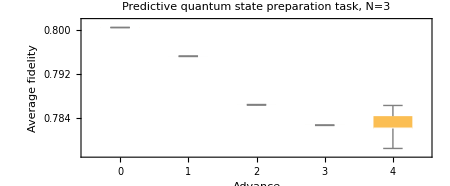

```mathematica
plotCQ=BoxWhiskerChart[listresults,ImageSize->450,LabelStyle->15,FrameLabel->{"Advance","Average fidelity"},PlotLabel->"Predictive quantum state preparation task, N=3",AspectRatio->1/(1+Sqrt[2]),ChartLabels->listadvance]
```

### Show the result

```mathematica
plotCQ
```

-Graphics-

## 2.3 Panel b (computed in its own notebook)

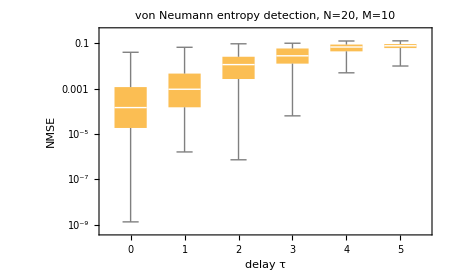
```mathematica
plot2=-Graphics-;
```

## 2.4 Figure 5

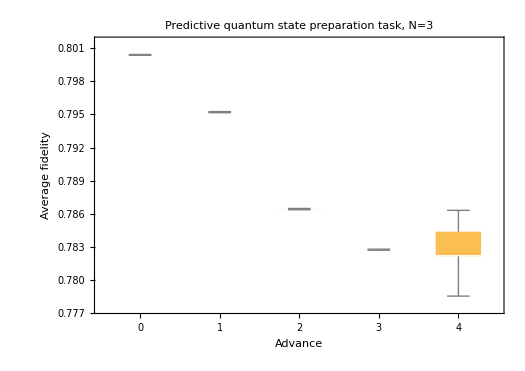
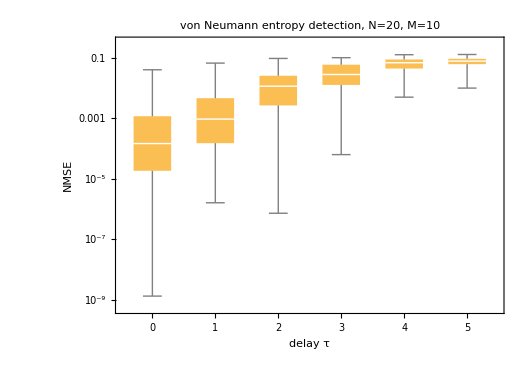
a |  | b
-Graphics- |  | -Graphics-

```mathematica
s=Spacer[30];
aspect=AspectRatio->1/(Sqrt[2]);
plotcombo=Grid[
{{Style["a",20,Bold],"",Style["b",20,Bold]},{Show[plotCQ,ImageSize->525,aspect],s,Show[plot2,ImageSize->525,aspect]}},Alignment->Left
]
```